```mathematica
SetDirectory@NotebookDirectory[];
$PlotTheme="Scientific";
<<"../hydrometallurgy-schema/src/concentration_parsing.wl"
```

## Some preliminary data distribution checks

### Do we need to keep track of concentration?

Of the 1104 reported D values, only 407 of them report the initial concentration of the metal.  When they do, these tend to be small, mostly 1 kBq/mL, less frequently 4.5 kBq/mL, and infrequently 9 kBq/mL for the two metal species.  Just to get a sense of the concentration levels here, let’s evaluate this:

```mathematica
/
EntityValue[
IsotopeData[{"Am",241}],
EntityProperty["Isotope","MolarRadioactivity"]]//UnitConvert[#,"Molar"]&
```

3.268×10^-8 M

```mathematica
/
EntityValue[
IsotopeData[{"Eu",152}],
EntityProperty["Isotope","MolarRadioactivity"]]//UnitConvert[#,"Molar"]&
```

1.0227×10^-9 M

Conclusion:  This is a very small quantity (much smaller than our ligand concentrations), and so we can exclude this in our modeling tasks (giving us more data); in other words, our model will assume that D is independent of the concentration, provided it is in the range of these studies (i.e., small).

### Time

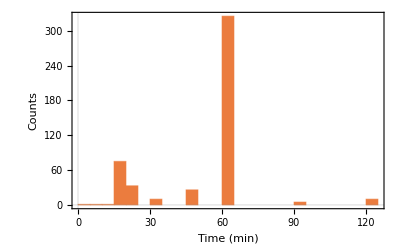

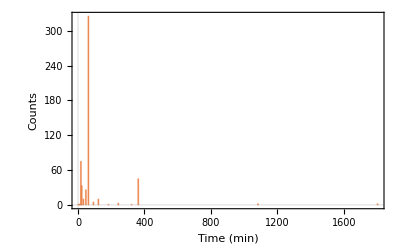

```mathematica
Clear[lookupTimes,times]

lookupTimes[f_?FileExistsQ]:=Lookup[#,"quantity",Nothing]&@Lookup[#,"time",Nothing]&@Lookup[#,"reaction conditions",Nothing]&@Import[f,"RawJSON"]

times=FileSystemMap[lookupTimes,".",FileNameForms->"ST*.json"];

Histogram[
DeleteMissing@Flatten@Values@times,
Automatic,Automatic,
FrameLabel->{"Time (min)","Counts"}]

Show[%,PlotRange->All]
```

## Temperature

```mathematica
lookupTemperature[f_?FileExistsQ]:=Lookup[#,"quantity",Nothing]&@Lookup[#,"temperature",Nothing]&@Lookup[#,"reaction conditions",Nothing]&@Import[f,"RawJSON"]

temps=FileSystemMap[lookupTemperature,".",FileNameForms->"ST*.json"];
```

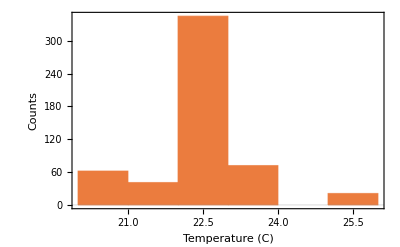

```mathematica
Histogram[
DeleteMissing@Flatten@Values@temps,
Automatic,Automatic,
FrameLabel->{"Temperature (C)","Counts"}]
```

### Extractants

```mathematica
lookupExtractant[f_?FileExistsQ]:=Lookup[#,"identity",Nothing]&/@Lookup[#,"extractants",Nothing]&@Lookup[#,"organic phase",Nothing]&@Import[f,"RawJSON"]
```

```mathematica
ex=FileSystemMap[lookupExtractant,".",FileNameForms->"ST*.json"];
```

How many unique (organic-soluble) extractants are present?

```mathematica
Length@DeleteDuplicates@Flatten@Values@ex
```

68

How often are they present (how many experiments?)

```mathematica
TableForm[
List@@@Normal@ReverseSort@Counts@Flatten@Values@ex]
```

TODGA | 195
tBu-CyMe4-BTBP | 32
CyMe4-BTTP | 29
2-bromodecanoic acid | 25
T8-PHEN-TAM | 20
T8-PHEN-CAM | 19
MeCyMe4-BTBP | 16
TWE-18 | 16
Br-Cosan | 15
CA-BTBP | 14
N-DP(DOM)P | 12
DMDOHEMA | 12
3-Me-N-DPP | 10
3,5-diMe-N-DPPz | 9
CA-BTP | 8
CyMe4-hemi-BTBP | 8
TWE-36 | 6
TWE-35 | 6
TWE-34 | 6
TWE-33 | 6
TWE-30 | 6
TWE-29 | 6
TWE-28 | 6
TWE-27 | 6
TWE-24 | 6
TWE-23 | 6
3-Me-N-DP(DOM)P | 6
TWE-22 | 6
TWE-21 | 6
Cy5S-Me4-BTBP | 6
CyMe4-BTPhen | 6
2PQM | 6
3,5-diMe-N-DPP | 6
TWE-17 | 6
TWE-15 | 6
TWE-14 | 6
TWE-11 | 6
2-bromohexanoic acid | 6
TWE-20 | 5
EsPyTri | 5
CyMe4-BTBP | 5
Cy5-S-Me4-BTBP | 5
Cy5-O-Me4-BTBP | 5
N-DPP | 5
TWE-19 | 4
T8-THP-TAM | 4
T8-THP-CAM | 4
CHELI2 | 3
NOMPIC | 2
NDMPIC | 2
TWE-16 | 2
TWE-10 | 2
TWE-9 | 2
TWE-8 | 2
TWE-7 | 2
TWE-6 | 2
TWE-2 | 2
TWE-1 | 2
3-Me-N-DPPz | 1
PPPA | 1
PPA | 1
TBADIPIC | 1
OPYR | 1
NOCPIC | 1
NDDIPIC | 1
CHELI1 | 1
2DOQA | 1
TBAPYR | 1

How many times do we have a single extractant or multiple extractants or an extractant plus phase modifier?

```mathematica
N@ResourceFunction["Proportions"]@Flatten@Values@Map[Length,ex,{2}]
```

<|1→0.848754,2→0.151246|>

### Holdback agents

```mathematica
lookupAqueousSolutes[f_?FileExistsQ]:=Lookup[#,"identity",Nothing]&/@Lookup[#,"solutes",Nothing]&@Lookup[#,"aqueous phase",Nothing]&@Import[f,"RawJSON"]

hb=FileSystemMap[lookupAqueousSolutes,".",FileNameForms->"ST*.json"]/.{"NH4NO3"->Nothing,"HNO3"->Nothing,"LiNO3"->Nothing};
```

70% of the reported entries have no aqueous holdback agent; other cases contain only one holdback agent.

Idea:  We could

```mathematica
N@ReverseSort@ResourceFunction["Proportions"]@Flatten[Values[hb],1]
```

<|{}→0.706406,{PyTri-Tetraol}→0.024911,{TWE-40}→0.024911,{SO3-Ph-BTBP}→0.0213523,{SO3-Ph-BTP}→0.0177936,{PHEN-6OH}→0.0177936,{TWE-42}→0.0177936,{TWE-41}→0.0177936,{TWE-38}→0.0142349,{TWE-37}→0.0142349,{PHEN-dialcohol}→0.0142349,{TWE-31}→0.0142349,{TWE-26}→0.0142349,{(PhSO3Na)2-BTPhen}→0.0142349,{(PhSO3Na)2-BTBP}→0.0142349,{CITAM}→0.0106762,{Phen-dialcohol}→0.0106762,{PyTri-diol}→0.0106762,{TWE-32}→0.00711744,{TWE-39}→0.00711744,{Phen-6OH}→0.00533808|>

### Solvents

```mathematica
lookupSolvents[f_?FileExistsQ]:=
Lookup[#,"solvents",Nothing]&@Lookup[#,"organic phase",Nothing]&@Import[f,"RawJSON"]
```

```mathematica
solv=FileSystemMap[lookupSolvents,".",FileNameForms->"ST*.json"];
```

How many have one solvent versus two solvents?

```mathematica
N@ResourceFunction["Proportions"]@Flatten@Values@Map[Length,solv,{2}]
```

<|2→0.368327,1→0.631673|>

## Tabularize the Data

What are our preliminary desiderata?

Extractant identity --> fingerprints and descriptors

Solvent-->some type of featurization?

Metal (only two, so no need for fancy descriptors)

D value

pH?

Temperature?

Time?

```mathematica
(*create a dictionary of each chemical name to its corresponding SMILES*)
chemRecord[entry_Association]:=
Association@Thread[ (entry["names"] ->  entry["SMILES"])]

chemRecord[d_List]:=Join@@chemRecord/@d

(*define a chemical records to be used later*)
chemicals = chemRecord@Import["chemical_record.json","RawJSON"];
```

```mathematica
molarity[c_Association]:=N@QuantityMagnitude@toMolarity@parseQuantity[c]
molarity[_?MissingQ]:=Missing[]

chemicalInfo[chemicals_Association][{}]:={Missing[],0.}

chemicalInfo[chemicals_Association][species_Association]:=With[
{smiles=Lookup[chemicals, species["identity"]],
conc = molarity@species["concentration"]},
{smiles,conc}]

extractants[chem_Association][r_Association]:=With[
{l=Query["organic phase","extractants",All,{"identity","concentration"}]@r},
Flatten@Take[#,2]&@Append[{Missing[],0.}]@ReverseSortBy[Last]@Map[chemicalInfo[chem]]@l]

temperature[r_Association]:=With[
{t = Query["reaction conditions","temperature"]@r},
If[MissingQ[t],
Missing[],
QuantityMagnitude@UnitConvert[#,"DegreesCelsius"]&@ parseQuantity@t]]

time[r_Association]:=With[
{t=Query["reaction conditions","time"]@r},
If[MissingQ[t],
Missing[],
QuantityMagnitude@UnitConvert[#,"Minutes"]&@parseQuantity@t]]

(*these are the only nitrate salts in ACSEPT*)

Clear[nitrateConc]
nitrateConc["KNO3",c_?NumericQ]:=c
nitrateConc["NH4NO3",c_?NumericQ]:=c
nitrateConc["HNO3",c_?NumericQ]:=c
nitrateConc["LiNO3",c_?NumericQ]:=c
nitrateConc[_,c_]:=0
nitrateConc[_,_?MissingQ]:=0.
nitrateConc[_?MissingQ]:=0.
nitrateConc[_,_String]:=0.


nitrateConc[r_Association]:=With[
{solutes=Query["aqueous phase","solutes"]@r,
 (* only nitric acid is used; if pH is specified but not HNO3 concentration, then infer nitrate contribution;
this is the case for ST106; otherwise return zero, as this will be captured in the explicit nitrate species*)
nitrateFromAcid = If[pHQ[r]&&!acidQ[r],acidConc[r] ,0]
},
nitrateFromAcid+Total@Map[nitrateConc[#["identity"], molarity@#["concentration"]]&]@solutes]


(*query if pH or acid concentration information is present*)
pHQuery = Query["aqueous phase","pH"]; 
acidQuery = Query["aqueous phase","solutes",SelectFirst[#identity == "HNO3"&]];

holdbackAgentQuery=Query["aqueous phase","solutes",
Select[FreeQ[#["identity"]]@{"KNO3","NH4NO3","HNO3","LiNO3"}&]];

holdbackAgent[chemicals_Association][r_Association]:=
chemicalInfo[chemicals]@First[#,{}]&@holdbackAgentQuery[r]

pHQ[r_Association]:=Not@MissingQ@pHQuery@r
acidQ[r_Association]:=Not@MissingQ@Query["concentration"]@acidQuery@r

(*return a molar concentration depending on what info is present;
stated initial pH takes precedent*)
acidConc[r_?pHQ]:=N@10^(-#)&@ pHQuery@r
acidConc[r_?acidQ]:=N@ molarity@Query["concentration"]@acidQuery@r
acidConc[_]:=Missing[]

(* ACSEPT is reported entirely as D (not logD), so we need only look this up and convert*)

(*process each entry*)
Clear[logD]
logD[{element_String,d_?PossibleZeroQ}]:=logD[{element,10^-4.}]
logD[{element_String,d_?NumericQ}]:={removeOxidation[element],Log[10.,d]}
logD[{element_,d_?MissingQ}]:=Nothing

(*process a record*)
logD[r_Association]:=logD/@Values/@Query["metals",All,{"identity","D"}]@r


(*clean up formatting to constant lower-case and remove TPH fraction information*)
formatSolvents[s_String]:=StringReplace["tph "~~___->"tph"]@ToLowerCase@s
formatSolvents[s_]:=s
SetAttributes[formatSolvents,Listable]

(*write this as major/ minor components and mole fraction*)
(*there are only two solvents (at most); so tabularize by adding a blank entry if needed*)
solvents[r_Association]:=With[
{l=Query["organic phase","solvents",All,{"identity","volfraction"}]@r},
formatSolvents@Flatten@Take[#,2]&@Append[{Missing[],0.}]@ReverseSortBy[Last]@Values@l]

(*we will want to exclude records that contain multiple extractants or holdback agents*)
containsHoldBackAgentQ[r_Association]:=With[
{aqSolutes = Query["aqueous phase","solutes",All,"identity"]@r},
Not@ContainsOnly[{"KNO3","NH4NO3","HNO3","LiNO3"}]@aqSolutes]

containsOneExtractantQ[r_Association]:=With[
{extractants = Query["organic phase","extractants",All,"identity"]@r},
EqualTo[1]@Length@extractants]


onlyOneExtractantAndNoHoldbackQ[r_Association]:=containsOneExtractantQ[r]&&Not[containsHoldBackAgentQ[r]]


Clear[tabularize]
(*you could put a pattern on the r argument to restrict it t only containing one extrantant or no holdback agent, but I'm gonna let it roll*)
tabularize[chemicals_Association][r_Association]:=With[
{observedDValues=logD[r],
experimentalConditions=Flatten@Through[
{extractants[chemicals],holdbackAgent[chemicals],
acidConc,nitrateConc,solvents,temperature,time}[r]]},
(*return each D and its conditions as rows*)
Join[experimentalConditions,#]&/@observedDValues]

(*
(*otherwise drop the record*)
tabularize[chemicals_Association][r_Association]:=Nothing
*)

(* a list of experimental records in a file*)
tabularize[chemicals_Association][r_List]:=Join@@tabularize[chemicals]/@r

(*a specific file*)
tabularize[chemicals_Association][f_?FileExistsQ]:=Prepend[f]/@tabularize[chemicals]@Import[f,"RawJSON"]

(*all files matching a pattern in the current directory*)
tabularize[chemicals_Association][pattern_String:"ST*.json"]:=Join@@
FileSystemMap[tabularize[chemicals],".",FileNameForms->pattern]


(*test inclusion/exclusion with patterns*)
(*
TestReport@
{VerificationTest[ Length@tabularize[chemicals]["ST1.json"],4], (*simple extraction*)
VerificationTest[ Length@tabularize[chemicals]["ST25.json"],0], (*two extractants should be excluded*)
VerificationTest[ Length@tabularize[chemicals]["ST100.json"],8] (*extraction with holdback agent*)
}
*)
```

### Data export

```mathematica
d=tabularize[chemicals]["ST*.json"];
Length[d]

Export["tabularized_results.csv",
d/.Missing[]->"",
TableHeadings->{"file","extractant1","extractant1 conc. (M)",
"extractant2","extractant2 conc. (M)",
"holdback","holdback conc. (M)",
"acid conc. (M)","nitrate conc. (M)",
"solvent1","solvent1 vol fraction",
"solvent2","solvent2 vol fraction",
"temperature (C)","time (min)",
"metal","logD"}]
```

1104

tabularized_results.csv

Caveats:
- Nitrate concentration is poorly defined; there are examples like ST106 in which HNO3 is specified as an acid, but the amount is implied only by the pH